## Variance of Variance within Large Normally Distributed Samples

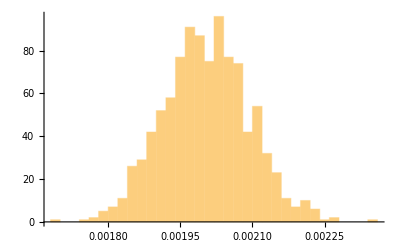

```mathematica
Table[Variance[Variance[RandomVariate[NormalDistribution[],{1000,1000}]]], {1000}] // Histogram
```

```mathematica
Table[Variance[Variance[RandomVariate[NormalDistribution[],{1000,1000}]]], {1000}] // FindDistribution
```

NormalDistribution[0.00200357,0.0000879336]

## Variance of Variance within Small Normally Distributed Sample

Note that there is no stable value of the variance of variances within the small sample.

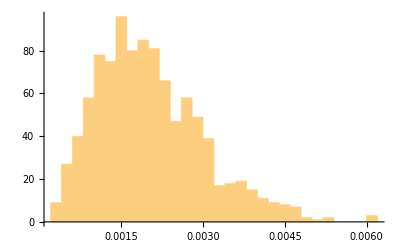

```mathematica
Table[Variance[Variance[RandomVariate[NormalDistribution[],{1000,10}]]], {1000}] // Histogram
```

```mathematica
Table[Variance[Variance[RandomVariate[NormalDistribution[],{1000,10}]]], {1000}] // FindDistribution
```

GammaDistribution[4.74135,0.000428028]